```mathematica
A = {{2,4,-1},{-3,-1,-2},{5,-2,1}};
B = {{4,-2,1},{1,-5,-5},{-5,3,-4}};
MatrixForm[A]
MatrixForm[B]
```

(2 | 4 | -1
-3 | -1 | -2
5 | -2 | 1)

(4 | -2 | 1
1 | -5 | -5
-5 | 3 | -4)

```mathematica
A. B - B. A
```

{{-2,-43,-15},{5,-14,6},{52,18,16}}

```mathematica
A = {{1,0,0,1},{0,1,1,1},{1,0,1,0},{1,0,0,2}};
MatrixForm[A]
```

(1 | 0 | 0 | 1
0 | 1 | 1 | 1
1 | 0 | 1 | 0
1 | 0 | 0 | 2)

```mathematica
MatrixForm[Inverse[A]]
```

(2 | 0 | 0 | -1
3 | 1 | -1 | -2
-2 | 0 | 1 | 1
-1 | 0 | 0 | 1)

```mathematica
A = {{-0.8,-8.4,-8.4},{-0.8,-3.4,-4.4},{1,5.2,6.2}};
MatrixForm[A]
```

(-0.8 | -8.4 | -8.4
-0.8 | -3.4 | -4.4
1 | 5.2 | 6.2)

```mathematica
MatrixForm[MatrixPower[A,2]]
MatrixForm[MatrixPower[A,10]]
MatrixForm[MatrixPower[A,50]]
```

(-1.04 | -8.4 | -8.4
-1.04 | -4.6 | -5.6
1.24 | 6.16 | 7.16)

(-0.0355457 | -0.249554 | -0.249554
-1.00584 | -4.04107 | -5.04107
1.01178 | 4.08277 | 5.08277)

(-4.84542×10^-11 | -3.39308×10^-10 | -3.39265×10^-10
-1. | -4. | -5.
1. | 4. | 5.)

```mathematica
MatrixForm[MatrixPower[A,100]]
```

(4.26328×10^-14 | 1.70531×10^-13 | 2.13164×10^-13
-1. | -4. | -5.
1. | 4. | 5.)

```mathematica
MatrixForm[MatrixPower[A,1000]]
```

(1.06581×10^-13 | 4.26326×10^-13 | 5.32907×10^-13
-1. | -4. | -5.
1. | 4. | 5.)

```mathematica
A = {{4,-5,4,4},{-1,1,2,2},{3,-4,6,6},{-3,3,6,6}};
MatrixForm[A]
```

(4 | -5 | 4 | 4
-1 | 1 | 2 | 2
3 | -4 | 6 | 6
-3 | 3 | 6 | 6)

```mathematica
X = {{x1},{x2},{x3},{x4}}
```

{{x1},{x2},{x3},{x4}}

```mathematica
b = {{2},{5},{7},{15}}
```

{{2},{5},{7},{15}}

```mathematica
MatrixForm[A. X]
```

(4 x1-5 x2+4 x3+4 x4
-x1+x2+2 x3+2 x4
3 x1-4 x2+6 x3+6 x4
-3 x1+3 x2+6 x3+6 x4)

```mathematica
x1=s
x3 = t
```

s

t

```mathematica
Solve[ A. X == b]
```

{{x2→8/7+(6 s)/7,x4→27/14+s/14-t}}

```mathematica
A = {{4,-1,k},{4,0,-3},{-1,2,0}};
Solve[Det[A] == 0]
```

{{k→-21/8}}

```mathematica
tredjegradspolynom [x_] := c0+c1 x + c2 x^2 + c3 x^3
```

```mathematica
tredjegradspolynom[x]
```

c0+c1 x+c2 x^2+c3 x^3

```mathematica
losning = Solve[{tredjegradspolynom[1]==5, tredjegradspolynom[2]==23, tredjegradspolynom[3]==69,tredjegradspolynom[4]==155}, {c0,c1,c2,c3}]
```

{{c0→3,c1→-2,c2→2,c3→2}}

{{-2,-Sin[2]},{-1,-Sin[1]},{0,0},{1,Sin[1]},{2,Sin[2]}}

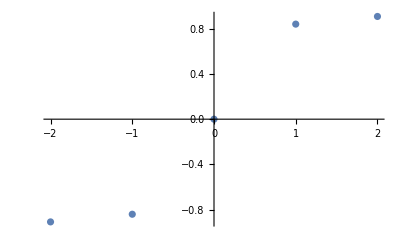

-2.98393×10^-16+0.970412 x+1.81065×10^-17 x^2-0.128941 x^3+1.29033×10^-17 x^4

```mathematica
minapunkter = Table[{x,Sin[x]},{x,-2,2}]
minbild1 = ListPlot[minapunkter]
minfunktion = Fit[minapunkter, {1,x,x^2,x^3,x^4},x]
```

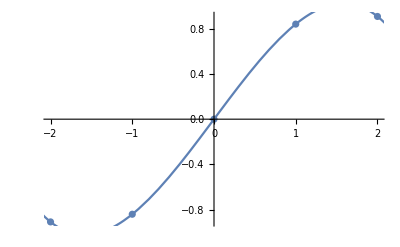

```mathematica
minbild2 = Plot[minfunktion, {x,-3,3}];
Show[minbild1,minbild2]
```

```mathematica
GG1={{-10.,109.07969834510772},{-9.9,107.17428272305513},{-9.8,105.03857986769091},{-9.7,102.5745519814992},{-9.6,99.68335693609163},{-9.5,98.0793017052489},{-9.4,95.956555741196},{-9.3,92.85275267883526},{-9.2,91.14439886496893},{-9.1,89.06326932816437},{-9.,86.67840530433615},{-8.9,83.8115383603627},{-8.8,82.90597512224836},{-8.7,79.67367648992764},{-8.6,78.75344810438511},{-8.5,76.96388138773543},{-8.4,74.62114409582871},{-8.3,72.5334275032322},{-8.2,69.55803653275302},{-8.1,68.15394453943703},{-8.,67.20618559679247},{-7.9,64.75897010275249},{-7.8,62.28069608702511},{-7.699999999999999,61.05844305028161},{-7.6,59.2807450887887},{-7.5,57.30988882316169},{-7.4,55.931365257253546},{-7.3,54.26380245430828},{-7.199999999999999,53.49866437247365},{-7.1,50.75580530025401},{-7.,49.20195035799177},{-6.9,47.3746789083477},{-6.8,45.77209200894006},{-6.699999999999999,44.68068782471552},{-6.6,42.23804103482046},{-6.5,41.76176234838952},{-6.4,39.904390200300206},{-6.3,38.29524835140627},{-6.199999999999999,37.88422233868392},{-6.1,35.72283231733743},{-6.,34.88840661753348},{-5.8999999999999995,33.43387922163262},{-5.8,32.26594873053972},{-5.7,31.04099316682072},{-5.6,28.948488704370266},{-5.5,27.814156756922067},{-5.3999999999999995,26.881415414396965},{-5.3,25.83412444896807},{-5.199999999999999,24.094475218127354},{-5.1,23.92141280659861},{-5.,22.910504497707347},{-4.8999999999999995,20.40651796457755},{-4.8,19.93391671199813},{-4.699999999999999,20.186512706800947},{-4.6,17.887415340467406},{-4.5,16.98251478501052},{-4.3999999999999995,16.17874473407001},{-4.3,15.994263145039127},{-4.199999999999999,15.602695757108874},{-4.1,14.180660153999993},{-4.,11.795428430231892},{-3.8999999999999995,12.199990304804208},{-3.8,11.286276811509875},{-3.6999999999999993,9.758138646693244},{-3.5999999999999996,9.33504727984977},{-3.5,8.887576488054874},{-3.3999999999999995,8.836409933412085},{-3.3,7.413470276166394},{-3.1999999999999993,6.427292159352066},{-3.0999999999999996,5.903734567390698},{-3.,6.617891559340828},{-2.8999999999999995,4.7126247371810015},{-2.8,4.573464154833675},{-2.6999999999999993,4.193111636346459},{-2.5999999999999996,4.352031286662221},{-2.5,2.878757501346356},{-2.3999999999999995,2.9394809314958295},{-2.3,3.41666646357334},{-2.1999999999999993,2.166705433515465},{-2.0999999999999996,1.6386218145450333},{-2.,2.0289608849360317},{-1.9000000000000004,1.2710406589849508},{-1.799999999999999,0.8859988283681465},{-1.6999999999999993,0.24839489939747272},{-1.5999999999999996,0.4605246893849403},{-1.5,-0.14690268743188498},{-1.4000000000000004,-0.23500025532090948},{-1.299999999999999,-0.934247676887588},{-1.1999999999999993,-0.9093840368578454},{-1.0999999999999996,-0.06786204366602822},{-1.,-0.6487245713941537},{-0.9000000000000004,-0.5071845546388688},{-0.7999999999999989,0.23735561263404437},{-0.6999999999999993,0.05509783596606943},{-0.5999999999999996,-0.5758821799735795},{-0.5,-0.32685735674778527},{-0.3999999999999986,-0.24148318507233857},{-0.29999999999999893,0.5667261992030082},{-0.1999999999999993,0.007526480553461168},{-0.09999999999999964,0.600529633879808},{0.,1.1616423358660302},{0.10000000000000142,0.03480711360401584},{0.20000000000000107,1.5327494971867943},{0.3000000000000007,1.354340412351819},{0.40000000000000036,1.0411003848199605},{0.5,1.7514804618686501},{0.6000000000000014,1.3180800187125103},{0.7000000000000011,1.9987008108233595},{0.8000000000000007,3.195150080657231},{0.9000000000000004,3.700355835664271},{1.,3.979476088922043},{1.1000000000000014,4.006754621369464},{1.200000000000001,4.155882077127413},{1.3000000000000007,5.037788552078741},{1.4000000000000004,5.9800992657645615},{1.5,7.038670537619401},{1.6000000000000014,7.067372884602802},{1.700000000000001,7.713068261892893},{1.8000000000000007,8.032494163681068},{1.9000000000000004,8.816084796429358},{2.,9.857475230663354},{2.1000000000000014,10.966235543857115},{2.200000000000001,11.058301072289312},{2.3000000000000007,12.239695551640269},{2.4000000000000004,12.911156949443713},{2.5,14.279048300201396},{2.6000000000000014,14.20708948320484},{2.700000000000001,15.96573798739859},{2.8000000000000007,15.982315396664214},{2.9000000000000004,17.26227166129302},{3.,18.16300199156804},{3.1000000000000014,18.69703509569974},{3.200000000000001,20.473120464763547},{3.3000000000000007,21.31832704046548},{3.4000000000000004,22.655235108023792},{3.5,23.09396537310865},{3.6000000000000014,24.229470062941758},{3.700000000000001,25.17972237637317},{3.8000000000000007,26.621428257202325},{3.9000000000000004,27.96786983736977},{4.,29.63930635363143},{4.100000000000001,30.496203203773156},{4.200000000000001,31.99174492433291},{4.300000000000001,32.66795716699084},{4.4,34.12563645456073},{4.5,36.566301661386966},{4.600000000000001,37.54080117311392},{4.700000000000001,38.6495952509737},{4.800000000000001,41.26084546596465},{4.9,42.3192123716446},{5.,42.92576968908325},{5.100000000000001,45.52952089181428},{5.200000000000001,46.36040434804982},{5.300000000000001,48.11279865357177},{5.4,49.07183688602118},{5.5,50.98439268821168},{5.600000000000001,53.13828539692712},{5.700000000000001,53.840805996279144},{5.800000000000001,56.42944834779449},{5.9,57.68597460515143},{6.,59.86427189018932},{6.100000000000001,62.2503483907316},{6.199999999999999,62.41081134850291},{6.300000000000001,65.30297755883196},{6.400000000000002,66.5745048649533},{6.5,69.8296006520878},{6.600000000000001,71.14261147694204},{6.699999999999999,73.38337509317111},{6.800000000000001,74.96189543393487},{6.900000000000002,76.24776250818473},{7.,78.21333126230081},{7.100000000000001,80.59938282607308},{7.199999999999999,82.45401906195865},{7.300000000000001,85.00963664699631},{7.400000000000002,87.02480913695952},{7.5,89.28148746636624},{7.600000000000001,91.45847873436058},{7.699999999999999,93.37457532153151},{7.800000000000001,95.82193076173786},{7.900000000000002,98.32179248390513},{8.,100.27493979914364},{8.100000000000001,102.20741746804234},{8.2,105.27341589465502},{8.3,107.40073870884792},{8.400000000000002,110.15164955955964},{8.5,112.35475462194312},{8.600000000000001,114.04179039749957},{8.7,117.19930855369702},{8.8,119.52143064560825},{8.900000000000002,121.00593339923239},{9.,123.96715841176169},{9.100000000000001,127.81341958095521},{9.200000000000003,130.15517871371975},{9.3,133.1604879098826},{9.400000000000002,134.37220267058134},{9.5,138.13341637777972},{9.600000000000001,140.21697859914556},{9.700000000000003,142.7930643356217},{9.8,145.60174050111482},{9.900000000000002,149.12412892334524},{10.,150.55060576784112}};
```

```mathematica
GG2={{-10.,-20.86680216055309},{-9.9,-20.276772424040505},{-9.8,-20.408339917470776},{-9.7,-19.935761996695984},{-9.6,-20.80469293861549},{-9.5,-19.784263010740798},{-9.4,-20.340623239310204},{-9.3,-19.802069762651747},{-9.2,-18.19746300546874},{-9.1,-19.15708226829296},{-9.,-18.803694322474435},{-8.9,-18.314355176354493},{-8.8,-18.257513348052697},{-8.7,-18.204378178411194},{-8.6,-17.597276857433638},{-8.5,-16.822091022848277},{-8.4,-16.443654868047975},{-8.3,-17.19217698957044},{-8.2,-16.954386523590465},{-8.1,-17.08068950621564},{-8.,-16.683721684676865},{-7.9,-16.24772607664686},{-7.8,-15.017052319690887},{-7.699999999999999,-15.838015837399597},{-7.6,-16.058636252202124},{-7.5,-16.243035618383708},{-7.4,-15.530438981358373},{-7.3,-15.788263459485213},{-7.199999999999999,-14.26296494073506},{-7.1,-15.003979983896778},{-7.,-14.506877866687933},{-6.9,-14.344136796124223},{-6.8,-13.10475725928355},{-6.699999999999999,-13.759263587457674},{-6.6,-13.680293574583219},{-6.5,-13.25985579180061},{-6.4,-13.558176381957677},{-6.3,-13.364338730243286},{-6.199999999999999,-12.460093894446876},{-6.1,-12.833895453839418},{-6.,-11.8294894362657},{-5.8999999999999995,-11.932433827350609},{-5.8,-11.505124377754157},{-5.7,-11.500172249607939},{-5.6,-11.525597317804186},{-5.5,-10.557262514767382},{-5.3999999999999995,-10.837261835848608},{-5.3,-10.495702743230408},{-5.199999999999999,-9.948142326161257},{-5.1,-10.445291580345318},{-5.,-9.579512281231233},{-4.8999999999999995,-10.290906444461507},{-4.8,-10.102776780228897},{-4.699999999999999,-10.47956342959292},{-4.6,-9.679652718692932},{-4.5,-9.37907890182633},{-4.3999999999999995,-9.895156602828152},{-4.3,-8.393492106749434},{-4.199999999999999,-8.111082541597813},{-4.1,-8.82240674119509},{-4.,-9.97193974105853},{-3.8999999999999995,-8.421158771202858},{-3.8,-7.940864686186718},{-3.6999999999999993,-7.3312042551871786},{-3.5999999999999996,-7.301831299983132},{-3.5,-7.122930804840791},{-3.3999999999999995,-6.912498269320832},{-3.3,-6.22274300774747},{-3.1999999999999993,-6.720367239338708},{-3.0999999999999996,-6.0703754467533635},{-3.,-6.5109886621053175},{-2.8999999999999995,-5.733589433242354},{-2.8,-6.648266106487953},{-2.6999999999999993,-4.755491561347791},{-2.5999999999999996,-4.295195395421572},{-2.5,-4.86557358194173},{-2.3999999999999995,-5.458546552531971},{-2.3,-4.701096997770241},{-2.1999999999999993,-5.060279722399738},{-2.0999999999999996,-2.9163208450851537},{-2.,-2.8458286214488524},{-1.9000000000000004,-3.4402660435307695},{-1.799999999999999,-3.119637445042608},{-1.6999999999999993,-3.639212998768268},{-1.5999999999999996,-3.497651507613422},{-1.5,-2.874724659246086},{-1.4000000000000004,-3.229340514285252},{-1.299999999999999,-2.1227659044262466},{-1.1999999999999993,-1.6474399072841952},{-1.0999999999999996,-1.9669216293091514},{-1.,-0.8609604985871492},{-0.9000000000000004,-1.6365045583769395},{-0.7999999999999989,-1.1017838238737423},{-0.6999999999999993,-0.7377999415258599},{-0.5999999999999996,-0.6871816220906666},{-0.5,-0.40820763008502664},{-0.3999999999999986,0.261169230276204},{-0.29999999999999893,-1.431264980283729},{-0.1999999999999993,0.055980569500252375},{-0.09999999999999964,-0.1387244109986457},{0.,0.5879949208203223},{0.10000000000000142,0.4960929852385299},{0.20000000000000107,1.1614414921701344},{0.3000000000000007,0.7456426665570899},{0.40000000000000036,1.693033732085071},{0.5,1.5950959798009952},{0.6000000000000014,1.751067686491175},{0.7000000000000011,2.0069510955802605},{0.8000000000000007,1.653661691348746},{0.9000000000000004,2.2781843294028272},{1.,2.4989925632284264},{1.1000000000000014,3.39291705579302},{1.200000000000001,2.725191670896511},{1.3000000000000007,3.008796831250094},{1.4000000000000004,3.0718346310569133},{1.5,3.199879563779542},{1.6000000000000014,3.5937292503377765},{1.700000000000001,3.4234669218836338},{1.8000000000000007,3.8530603770810212},{1.9000000000000004,3.773764876648574},{2.,4.917882668706809},{2.1000000000000014,4.572669508286796},{2.200000000000001,5.568238587463199},{2.3000000000000007,5.150705371565688},{2.4000000000000004,5.7398118840238235},{2.5,4.777275073170207},{2.6000000000000014,5.971321655492267},{2.700000000000001,6.542416054131718},{2.8000000000000007,6.453815569244777},{2.9000000000000004,5.989458395948998},{3.,6.695182226119071},{3.1000000000000014,6.399794218288693},{3.200000000000001,7.536959983661471},{3.3000000000000007,6.898822904535726},{3.4000000000000004,6.949527210463946},{3.5,8.211246257269142},{3.6000000000000014,8.292852823491248},{3.700000000000001,9.21506528155512},{3.8000000000000007,8.064455286691313},{3.9000000000000004,8.471308630080026},{4.,7.88739147511014},{4.100000000000001,8.394849837327017},{4.200000000000001,9.424869557296208},{4.300000000000001,9.2169801194976},{4.4,9.696733365559432},{4.5,9.116219696958987},{4.600000000000001,9.260458422662417},{4.700000000000001,10.588370134844418},{4.800000000000001,9.669873364048705},{4.9,11.17903019162198},{5.,10.755516080603607},{5.100000000000001,11.173949048493892},{5.200000000000001,10.973012361868342},{5.300000000000001,11.448145115561658},{5.4,11.755577405930952},{5.5,11.305912708191773},{5.600000000000001,11.975239078458614},{5.700000000000001,11.505332591637465},{5.800000000000001,12.533265698347565},{5.9,13.585883081612966},{6.,13.392871812316717},{6.100000000000001,13.068170724168757},{6.199999999999999,13.034386983982422},{6.300000000000001,13.903893379630968},{6.400000000000002,13.879682607334793},{6.5,14.619740957902726},{6.600000000000001,13.543577562109705},{6.699999999999999,14.688568089160697},{6.800000000000001,14.542357378208662},{6.900000000000002,14.942255632763333},{7.,15.156553314972228},{7.100000000000001,15.0986095502846},{7.199999999999999,14.788194510779721},{7.300000000000001,15.265918338908765},{7.400000000000002,16.2629337746521},{7.5,17.706207630957696},{7.600000000000001,16.103630609384393},{7.699999999999999,16.809154025294642},{7.800000000000001,16.66911761445867},{7.900000000000002,16.581827032297497},{8.,16.693716318193815},{8.100000000000001,18.207458229863747},{8.2,17.1827429480314},{8.3,18.677532389547892},{8.400000000000002,18.223815921486953},{8.5,18.136457363210464},{8.600000000000001,18.850028168718058},{8.7,18.566394022152696},{8.8,18.704480708661613},{8.900000000000002,18.013655666499677},{9.,19.097220763612054},{9.100000000000001,19.463852333985297},{9.200000000000003,19.66309995736593},{9.3,18.363189451779824},{9.400000000000002,19.90892994821389},{9.5,20.014235775707526},{9.600000000000001,19.646224465655852},{9.700000000000003,20.01823413342103},{9.8,20.756416512807032},{9.900000000000002,21.509523486872517},{10.,21.689457384540574}};
```

```mathematica
GG3={{-10.,-131320.73639177484},{-9.9,-124910.80603701764},{-9.8,-118753.37110784548},{-9.7,-112841.84835856495},{-9.6,-107168.55290918045},{-9.5,-101725.83614043363},{-9.4,-96506.81464438023},{-9.3,-91504.36633512122},{-9.2,-86711.9432134064},{-9.1,-82122.66992939071},{-9.,-77730.00844035955},{-8.9,-73527.62708020982},{-8.8,-69509.43961239123},{-8.7,-65668.91817753224},{-8.6,-62000.18080724667},{-8.5,-58497.70143824341},{-8.4,-55155.2941092319},{-8.3,-51967.81341774531},{-8.2,-48929.90673289776},{-8.1,-46035.6577526558},{-8.,-43280.49780297512},{-7.9,-40658.96859438007},{-7.8,-38166.139681527406},{-7.699999999999999,-35797.520199582636},{-7.6,-33548.07560006172},{-7.5,-31413.688612755665},{-7.4,-29389.23213886277},{-7.3,-27470.627039285453},{-7.199999999999999,-25654.044623930655},{-7.1,-23934.97604380928},{-7.,-22309.521397814104},{-6.9,-20773.647386151293},{-6.8,-19323.852180153663},{-6.699999999999999,-17956.547335913965},{-6.6,-16667.709846505397},{-6.5,-15454.234464321771},{-6.4,-14312.53326560003},{-6.3,-13239.587347809906},{-6.199999999999999,-12232.482091019947},{-6.1,-11287.377578634481},{-6.,-10401.902876792721},{-5.8999999999999995,-9573.155843219285},{-5.8,-8798.104049295112},{-5.7,-8074.517087629583},{-5.6,-7399.131754008451},{-5.5,-6770.219726020624},{-5.3999999999999995,-6184.973348338681},{-5.3,-5640.728896499672},{-5.199999999999999,-5135.988144980386},{-5.1,-4668.2305082410685},{-5.,-4235.233841730593},{-4.8999999999999995,-3835.1774107005776},{-4.8,-3466.121665970519},{-4.699999999999999,-3126.036885918308},{-4.6,-2813.348817016078},{-4.5,-2526.275712600318},{-4.3999999999999995,-2263.6440578406587},{-4.3,-2023.1802715590552},{-4.199999999999999,-1803.8177819981902},{-4.1,-1603.8777085109596},{-4.,-1422.2852960799282},{-3.8999999999999995,-1258.0204640011389},{-3.8,-1109.2205855774876},{-3.6999999999999993,-974.9529291404823},{-3.5999999999999996,-853.9540057273832},{-3.5,-745.5354058064842},{-3.3999999999999995,-648.5749403249868},{-3.3,-562.1009964975451},{-3.1999999999999993,-485.23667979260915},{-3.0999999999999996,-417.31690999547754},{-3.,-356.8886081831765},{-2.8999999999999995,-304.1075938179381},{-2.8,-257.99836792742326},{-2.6999999999999993,-217.4813814768474},{-2.5999999999999996,-182.4831923878991},{-2.5,-152.25891807423307},{-2.3999999999999995,-126.38846753569301},{-2.3,-104.03577675138499},{-2.1999999999999993,-85.03039896115186},{-2.0999999999999996,-69.15119920820648},{-2.,-55.77820919933243},{-1.9000000000000004,-44.68379288700334},{-1.799999999999999,-35.5655634242519},{-1.6999999999999993,-28.16872290827368},{-1.5999999999999996,-21.941579748604994},{-1.5,-17.046340684552106},{-1.4000000000000004,-13.284707678466328},{-1.299999999999999,-10.019062823843283},{-1.1999999999999993,-7.698311084948533},{-1.0999999999999996,-5.7696208909224795},{-1.,-4.35485708338285},{-0.9000000000000004,-3.2188592435882803},{-0.7999999999999989,-2.4658856560827496},{-0.6999999999999993,-1.877802367757061},{-0.5999999999999996,-1.1352199365951532},{-0.5,-1.0676880803910755},{-0.3999999999999986,-0.7526890645376803},{-0.29999999999999893,-0.17516809188750915},{-0.1999999999999993,-0.22466343185015553},{-0.09999999999999964,0.15251583668284135},{0.,0.35409803717501603},{0.10000000000000142,0.4074311172796028},{0.20000000000000107,0.7386886911000536},{0.3000000000000007,1.114341539835685},{0.40000000000000036,1.1776928283339783},{0.5,1.617219760834041},{0.6000000000000014,1.8863113599129244},{0.7000000000000011,2.2906633815677235},{0.8000000000000007,3.1555767267883383},{0.9000000000000004,3.762270062176354},{1.,4.947327549131238},{1.1000000000000014,6.312314907762644},{1.200000000000001,8.427936771747342},{1.3000000000000007,10.596768334686159},{1.4000000000000004,13.878917115741917},{1.5,17.74246447743925},{1.6000000000000014,22.686496339412244},{1.700000000000001,28.58207753449302},{1.8000000000000007,36.32031845516094},{1.9000000000000004,45.22197148588115},{2.,56.51315606104466},{2.1000000000000014,69.76034260565413},{2.200000000000001,85.75064149590084},{2.3000000000000007,104.60558421594664},{2.4000000000000004,126.85338454342073},{2.5,152.90789597268665},{2.6000000000000014,183.1161072763955},{2.700000000000001,218.15736848603368},{2.8000000000000007,258.5095663667585},{2.9000000000000004,304.7753731868828},{3.,357.51390372744544},{3.1000000000000014,417.65674098752453},{3.200000000000001,485.8607707378421},{3.3000000000000007,562.7779800234792},{3.4000000000000004,649.131132928216},{3.5,746.2327897662515},{3.6000000000000014,854.7145679452477},{3.700000000000001,975.3413834211548},{3.8000000000000007,1109.6415982322771},{3.9000000000000004,1258.5851199292456},{4.,1423.159021161965},{4.100000000000001,1604.7728521573154},{4.200000000000001,1804.412842021371},{4.300000000000001,2023.842702348836},{4.4,2263.9693177543836},{4.5,2527.055571650575},{4.600000000000001,2813.814777867331},{4.700000000000001,3126.6380599780287},{4.800000000000001,3466.6159848238735},{4.9,3835.5481730051265},{5.,4235.725118983329},{5.100000000000001,4668.946684118971},{5.200000000000001,5136.692878709377},{5.300000000000001,5641.312749710476},{5.4,6185.536260560237},{5.5,6770.912649571308},{5.600000000000001,7399.67001287992},{5.700000000000001,8074.893378807712},{5.800000000000001,8798.798850172561},{5.9,9573.717800473712},{6.,10402.667551379018},{6.100000000000001,11287.891843078884},{6.199999999999999,12232.798891854965},{6.300000000000001,13240.164640963352},{6.400000000000002,14313.210164631433},{6.5,15454.762204609047},{6.600000000000001,16668.200238745565},{6.699999999999999,17957.15662975224},{6.800000000000001,19324.323765002293},{6.900000000000002,20774.21948839259},{7.,22309.820813923998},{7.100000000000001,23935.45643622287},{7.199999999999999,25654.635029699337},{7.300000000000001,27471.224085095386},{7.400000000000002,29389.737906956758},{7.5,31413.981613500393},{7.600000000000001,33548.81362375129},{7.699999999999999,35798.12072870583},{7.800000000000001,38166.97648028197},{7.900000000000002,40659.45525881696},{8.,43281.203201856195},{8.100000000000001,46036.42292103836},{8.2,48930.46670299178},{8.3,51968.6962249992},{8.400000000000002,55155.90317489268},{8.5,58498.15238704621},{8.600000000000001,62000.73131691848},{8.7,65669.35019824388},{8.8,69509.86276363605},{8.900000000000002,73528.23529380036},{9.,77730.67613903432},{9.100000000000001,82123.22629231591},{9.200000000000003,86712.55400695626},{9.3,91504.99522068538},{9.400000000000002,96507.30688855133},{9.5,101726.16486608572},{9.600000000000001,107169.19986163896},{9.700000000000003,112842.8968610593},{9.8,118754.06438674928},{9.900000000000002,124911.20749346512},{10.,131321.46175885745}};
```

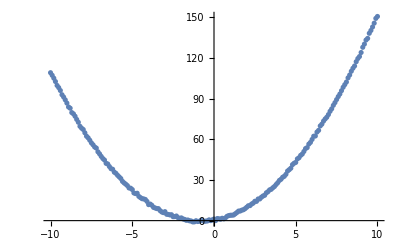

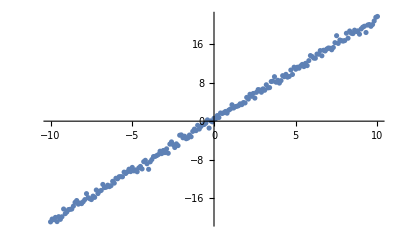

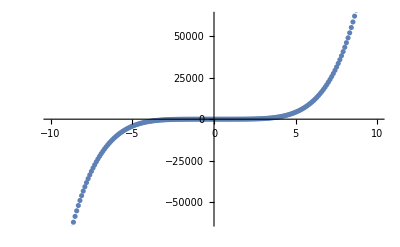

```mathematica
minPlotGG1 = ListPlot[GG1]
minPlotGG2 = ListPlot[GG2]
minPlotGG3 = ListPlot[GG3]
```

```mathematica
minFunktionGG1 = Fit[GG1, {1,x,x^2},x]
minFunktionGG2 = Fit[GG2, {1,x},x]
minFunktionGG3 = Fit[GG3, {1,x^2,x^3,x^4,x^5},x]
```

0.352676+2.0989 x+1.29944 x^2

0.296968+2.10212 x

0.311641-0.00131651 x^2+1.3748 x^3+0.0000141578 x^4+1.29942 x^5

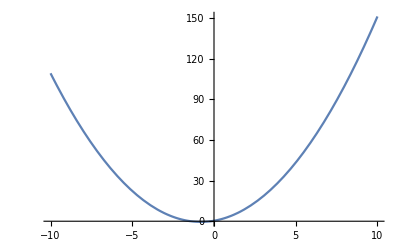

Show::gcomb: Could not combine the graphics objects in Show[,0.352676+2.0989 x+1.29944 x^2].

Show[-Graphics-,0.352676+2.0989 x+1.29944 x^2]

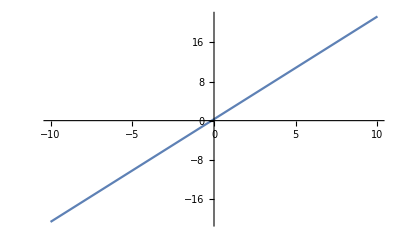

Show::gcomb: Could not combine the graphics objects in Show[0.296968+2.10212 x,].

Show[0.296968+2.10212 x,-Graphics-]

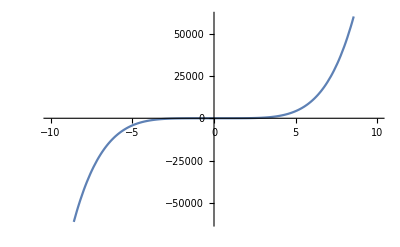

Show::gcomb: Could not combine the graphics objects in Show[0.311641-0.00131651 x^2+1.3748 x^3+0.0000141578 x^4+1.29942 x^5,].

Show[0.311641-0.00131651 x^2+1.3748 x^3+0.0000141578 x^4+1.29942 x^5,-Graphics-]

```mathematica
Plot[minFunktionGG1, {x,-10,10}]
Show[minPlotGG1, minFunktionGG1]
Plot[minFunktionGG2, {x,-10,10}]
Show[minFunktionGG2,minPlotGG2]
Plot[minFunktionGG3, {x,-10,10}]
Show[minFunktionGG3, minPlotGG3]
```